```mathematica
Clear["Global`*"]
```

```mathematica
(*Center equilibrium for cooperative specialization*)
S1 = v*s*(1−Α)+p*s*(1−α)+(1−v−p)*g*(1−δ) /. {Α-> ((Π/s) +s),α-> ((ψ/s) +s),δ-> ((Δ/g) +g)};
S2 = v*s*(1−α)+p*s*(1−Α)+(1−v−p)*g*(1−δ)/. {Α-> ((Π/s )+s),α-> ((ψ/s) +s),δ-> ((Δ/g) +g)};
S = u*(1-u)*(S1-S2);
S=Simplify[S];
SS = Simplify[S /. {p -> (p+1/2), v -> (v+1/2), u -> (u+1/2)}];
SS/.{v-> Subscript[v, 1],p-> Subscript[v, 2],Π -> π,Δ-> Subscript[π, g]};
H1=u*Π+(1−u)*ψ;
H2 =u* ψ+(1−u)*Π;
HG = Δ;
Hbar = v*H1+p*H2+(1-v-p)(HG);
V=v(H1-Hbar);
V=Simplify[V];
VS = Simplify[V /. {p -> (p+1/2), v -> (v+1/2), u -> (u+1/2)}];
VS /.{v-> Subscript[v, 1],p-> Subscript[v, 2],Π -> π,Δ-> Subscript[π, g]};
P = p(H2-Hbar);
P=Simplify[P];
PS = Simplify[P /. {p -> (p+1/2), v -> (v+1/2), u -> (u+1/2)}];
PS /.{v-> Subscript[v, 1],p-> Subscript[v, 2],Π -> π,Δ-> Subscript[π, g]};
```

```mathematica
J1= ({{D[SS,u], D[SS,v], D[SS,p]}, {D[VS,u], D[VS,v], D[VS,p]}, {D[PS,u], D[PS,v], D[PS,p]}})//MatrixForm
J1=Simplify[J1];
J = Simplify[J1/. {v-> 0,p-> 0, u -> 0}]
```

(-((-1/2+u) (p-v) (-1+α) (Π-ψ))/α-((1/2+u) (p-v) (-1+α) (Π-ψ))/α | ((-1/2+u) (1/2+u) (-1+α) (Π-ψ))/α | -((-1/2+u) (1/2+u) (-1+α) (Π-ψ))/α
1/2 v (2 p Π-2 (-1+v) Π-(2+2 p-2 v) ψ) | 1/2 v (2 Δ-(1+2 u) Π-(1-2 u) ψ)+1/2 (2 (-1+p+v) Δ+p (-1+2 u) Π-(1+2 u) (-1+v) Π-(-1+p+2 u+2 p u+v-2 u v) ψ) | 1/2 v (2 Δ+(-1+2 u) Π-(1+2 u) ψ)
1/2 p ((2 p-2 (1+v)) Π-(2 p-2 (1+v)) ψ) | 1/2 p (2 Δ+(-1-2 u) Π-(1-2 u) ψ) | 1/2 p (2 Δ+(-1+2 u) Π-(1+2 u) ψ)+1/2 (2 (-1+p+v) Δ+(1+p (-1+2 u)-v-2 u (1+v)) Π-(-1+p+2 p u+v-2 u (1+v)) ψ))

(0 | -((-1+α) (Π-ψ))/(4 α) | ((-1+α) (Π-ψ))/(4 α)
0 | 1/2 (-2 Δ+Π+ψ) | 0
0 | 0 | 1/2 (-2 Δ+Π+ψ))

```mathematica
Λ=({{1/2 (2 Δ-Π-ψ), 0, 0}, {0, 0, 1/2 (Π-ψ)}, {0, -1/2 (Π-ψ), 0}})
```

{{1/2 (2 Δ-Π-ψ),0,0},{0,0,(Π-ψ)/2},{0,1/2 (-Π+ψ),0}}

```mathematica
Eigensystem[J]
```

{{1/2 (2 Δ-Π-ψ),-1/2 ⅈ (Π-ψ),1/2 ⅈ (Π-ψ)},{{0,1,1},{ⅈ,-1,1},{-ⅈ,-1,1}}}

```mathematica
Eigensystem[Λ]
```

{{1/2 (2 Δ-Π-ψ),1/2 ⅈ (Π-ψ),1/2 ⅈ (-Π+ψ)},{{1,0,0},{0,-ⅈ,1},{0,ⅈ,1}}}

```mathematica
P=({{0, 1, 0}, {1, 0, -1}, {1, 0, 1}});
Pin=Inverse[P];
Simplify[Pin.J.P]
```

{{Δ-Π/2-ψ/2,0,0},{0,0,(Π-ψ)/2},{0,1/2 (-Π+ψ),0}}

```mathematica
ϕ = Simplify[({{SS}, {VS}, {PS}})-J.({{u}, {v}, {p}})]
```

{{-u^2 (p-v) (Π-ψ)},{1/2 (p u (Π-ψ)+u v (Π-ψ)+v^2 (2 Δ-(1+2 u) Π+(-1+2 u) ψ)+p v (2 Δ+(-1+2 u) Π-(1+2 u) ψ))},{1/2 (p u (-Π+ψ)+u v (-Π+ψ)+p v (2 Δ-(1+2 u) Π+(-1+2 u) ψ)+p^2 (2 Δ+(-1+2 u) Π-(1+2 u) ψ))}}

```mathematica
P.({{x}, {y}, {z}})
```

{{y},{x-z},{x+z}}

```mathematica
Φ=ϕ/.{u-> y, v->( x-z), p-> (x+z)}
```

{{-2 y^2 z (Π-ψ)},{1/2 (y (x-z) (Π-ψ)+y (x+z) (Π-ψ)+(x-z)^2 (2 Δ-(1+2 y) Π+(-1+2 y) ψ)+(x-z) (x+z) (2 Δ+(-1+2 y) Π-(1+2 y) ψ))},{1/2 (y (x-z) (-Π+ψ)+y (x+z) (-Π+ψ)+(x-z) (x+z) (2 Δ-(1+2 y) Π+(-1+2 y) ψ)+(x+z)^2 (2 Δ+(-1+2 y) Π-(1+2 y) ψ))}}

```mathematica
Φ2=Pin.Φ;
(*Pin.({{SS}, {VS}, {PS}})-({{xdot}, {ydot}, {zdot}});*)
```

```mathematica
h=a *y^2+b*y*z+c *z^2;
h2=a *y^2+b*y*z+c *z^2+d*y^3+e*z*y^2+f*y*z^2+g*z^3;
h3=a *y^2+b*y*z+c *z^2+d*y^3+e*z*y^2+f*y*z^2+g*z^3+e*y^4+f*y^3*z+g*y^2*z^2+i*y*z^3+j*z^4;
{xdot, ydot, zdot} = Λ.({{x}, {y}, {z}})+Φ2/.{x-> h};
(*Λ.({{x}, {y}, {z}});
xdot;*)
```

```mathematica
(*Expand[-xdot+({{D[h,y], D[h,z]}}).({{ydot}, {zdot}})]==Fullfxn;*)
```

```mathematica
D[h,y]
```

2 a y+b z

```mathematica
Collect[xdot/.{z-> 0}, y]
Collect[xdot/.{y-> 0}, z]
Collect[ydot/.{y-> 0}, z]
Collect[ydot/.{z-> 0}, y]
ydot/.{y-> 0, z-> 0};
zdot/.{y-> 0, z-> 0};
```

{1/2 a y^2 (2 Δ-Π-ψ)+y^4 (2 a^2 Δ-a^2 Π-a^2 ψ)+y^3 (1/2 a (Π-ψ)+1/2 a (-Π+ψ))}

{1/2 c z^2 (2 Δ-Π-ψ)+c^2 z^4 (2 Δ-Π-ψ)}

{1/2 z (Π-ψ)}

{0}

```mathematica
Fullfxn=Expand[-xdot+D[h,y]*ydot+zdot*D[h,z]];
```

```mathematica
Collect[Fullfxn, z^2]/.{y-> 0}
Collect[Fullfxn, y^2]/.{z-> 0}
Collect[Fullfxn, y*z]
```

{z^2 (-c Δ+(b Π)/2+(c Π)/2-(b ψ)/2+(c ψ)/2)+z^4 (2 c^2 Δ-c^2 Π-c^2 ψ)}

{y^2 (-a Δ+(a Π)/2-(b Π)/2+(a ψ)/2+(b ψ)/2)+y^4 (-2 a^2 Δ+a^2 Π-a b Π+a^2 ψ+a b ψ)}

{-a y^2 Δ-2 a^2 y^4 Δ-2 a b y^3 z Δ-c z^2 Δ+2 b c y z^3 Δ+2 c^2 z^4 Δ+1/2 a y^2 Π-1/2 b y^2 Π+a^2 y^4 Π-a b y^4 Π-6 a y^3 z Π+a b y^3 z Π-b^2 y^3 z Π-2 a c y^3 z Π+1/2 b z^2 Π+1/2 c z^2 Π-2 b y^2 z^2 Π-3 b c y^2 z^2 Π+2 c y z^3 Π-b c y z^3 Π-2 c^2 y z^3 Π-c^2 z^4 Π+1/2 a y^2 ψ+1/2 b y^2 ψ+a^2 y^4 ψ+a b y^4 ψ+6 a y^3 z ψ+a b y^3 z ψ+b^2 y^3 z ψ+2 a c y^3 z ψ-1/2 b z^2 ψ+1/2 c z^2 ψ+2 b y^2 z^2 ψ+3 b c y^2 z^2 ψ-2 c y z^3 ψ-b c y z^3 ψ+2 c^2 y z^3 ψ-c^2 z^4 ψ+y z (-b Δ+a Π+(b Π)/2-c Π-a ψ+(b ψ)/2+c ψ)}

```mathematica
z2=-c* Δ+(b* Π)/2+(c* Π)/2-(b* ψ)/2+(c* ψ)/2;
y2=-a* Δ+(a *Π)/2-(b* Π)/2+(a *ψ)/2+(b* ψ)/2;
yz=-b *Δ+a* Π+(b* Π)/2-c* Π-a *ψ+(b* ψ)/2+c* ψ;
Solve[{z2==0,y2==0,yz==0},{a,b,c}]
```

{{a→0,b→0,c→0}}

```mathematica
({{xdot}, {ydot}, {zdot}})/.{a-> 0, b-> 0, c-> 0}
```

{{{1/4 (z^2 (2 Δ-(1+2 y) Π+(-1+2 y) ψ)-z^2 (2 Δ+(-1+2 y) Π-(1+2 y) ψ))+1/4 (-z^2 (2 Δ-(1+2 y) Π+(-1+2 y) ψ)+z^2 (2 Δ+(-1+2 y) Π-(1+2 y) ψ))}},{{1/2 z (Π-ψ)-2 y^2 z (Π-ψ)}},{{1/2 y (-Π+ψ)+1/2 (-z^2 (2 Δ-(1+2 y) Π+(-1+2 y) ψ)+z^2 (2 Δ+(-1+2 y) Π-(1+2 y) ψ))}}}

```mathematica
newplot3={1/2 z (Π-ψ)-2 y^2 z (Π-ψ),1/2 y (-Π+ψ)+1/2 (-z^2 (2 Δ-(1+2 y) Π+(-1+2 y) ψ)+z^2 (2 Δ+(-1+2 y) Π-(1+2 y) ψ))}/.{ψ-> 1, Δ-> 1.5, Π-> 2.5}
```

{0.75 z-3. y^2 z,-0.75 y+1/2 ((2.-2 y+2.5 (-1+2 y)) z^2-(2.+2 y-2.5 (1+2 y)) z^2)}

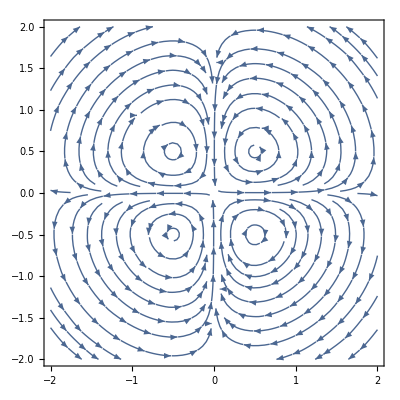

```mathematica
StreamPlot[newplot3,{z,-2,2},{y,-2,2}]
```

Now let’s try this guy out:

```mathematica
({{xdot}, {ydot}, {zdot}})/.{a-> 0, b-> 0, c-> 0}
```

{{{1/4 (z^2 (2 Δ-(1+2 y) Π+(-1+2 y) ψ)-z^2 (2 Δ+(-1+2 y) Π-(1+2 y) ψ))+1/4 (-z^2 (2 Δ-(1+2 y) Π+(-1+2 y) ψ)+z^2 (2 Δ+(-1+2 y) Π-(1+2 y) ψ))}},{{1/2 z (Π-ψ)-2 y^2 z (Π-ψ)}},{{1/2 y (-Π+ψ)+1/2 (-z^2 (2 Δ-(1+2 y) Π+(-1+2 y) ψ)+z^2 (2 Δ+(-1+2 y) Π-(1+2 y) ψ))}}}

```mathematica
newplot = {1/2 z (Π-ψ)-2 y^2 z (Π-ψ), 1/2 y (-Π+ψ)+1/2 (-z^2 (2 Δ-(1+2 y) Π+(-1+2 y) ψ)+z^2 (2 Δ+(-1+2 y) Π-(1+2 y) ψ))}/.{ψ-> 1, Δ-> 1.5, Π-> 2};
```

Now we’ll plot the stability:

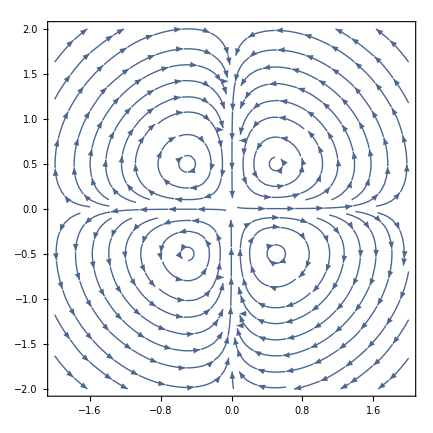

```mathematica
StreamPlot[newplot,{z,-2,2},{y,-2,2}]
```

```mathematica
(*Checking the Higher order terms: *)

h2=a *y^2+b*y*z+c *z^2+d*y^3+e*z*y^2+f*y*z^2+g*z^3;
{xdot, ydot, zdot} = Λ.({{x}, {y}, {z}})+ϕ/.{x-> h2};
Fullfxn=Expand[-xdot+D[h2,y]*ydot+zdot*D[h2,z]];
Fullfxn /. {a-> 0, b-> 0, c-> 0, d-> 0, e-> 0, f-> 0, g-> 0}
```

```mathematica
{0}
(*The story is the same! The center equilibrium is unstable!*)
```

```mathematica
newplot2 = {1/2 z (Π-ψ)-2 y^2 z (Π-ψ), 1/2 y (-Π+ψ)+1/2 (-z^2 (2 Δ-(1+2 y) Π+(-1+2 y) ψ)+z^2 (2 Δ+(-1+2 y) Π-(1+2 y) ψ))}/.{ψ-> 0.1, Δ-> 1.5, Π-> 1.6};
```

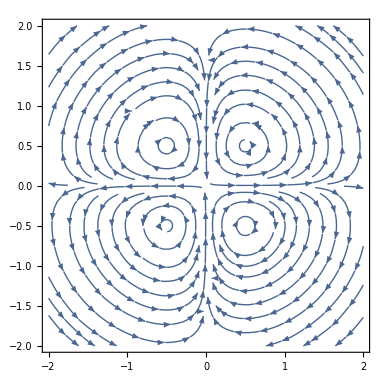

```mathematica
StreamPlot[newplot2,{z,-2,2},{y,-2,2}]
```

```mathematica
{xdot, ydot, zdot}/.{a-> 0, b-> 0, c-> 0, d-> 0, e-> 0, f-> 0, g-> 0};
{xdot2, ydot2, zdot2}={1/4 (z^2 (2 Δ-(1+2 y) Π+(-1+2 y) ψ)-z^2 (2 Δ+(-1+2 y) Π-(1+2 y) ψ))+1/4 (-z^2 (2 Δ-(1+2 y) Π+(-1+2 y) ψ)+z^2 (2 Δ+(-1+2 y) Π-(1+2 y) ψ)),1/2 z (Π-ψ)-2 y^2 z (Π-ψ),1/2 y (-Π+ψ)+1/2 (-z^2 (2 Δ-(1+2 y) Π+(-1+2 y) ψ)+z^2 (2 Δ+(-1+2 y) Π-(1+2 y) ψ))};
J2=({{D[ydot2, y], D[ydot2, z]}, {D[zdot2, y], D[zdot2, z]}})/.{z-> 0, y-> 0}
Eigenvalues[J2]
```

{{0,(Π-ψ)/2},{1/2 (-Π+ψ),0}}

{1/2 ⅈ (Π-ψ),-1/2 ⅈ (Π-ψ)}

Because these eigenvalues are in the opporite orders I’ll move the corresponding eigenvalues!

```mathematica
B=({{0, ⅈ, -ⅈ}, {1, -1, -1}, {1, 1, 1}}) (*Similarity Matrix for Matrix A *)
Bin=Inverse[B]
S=({{1, 0, 0}, {0, ⅈ, -ⅈ}, {0, 1, 1}})(*Similarity Matrix for Matrix Λ*)
Sinv=Inverse[S]
```

{{0,ⅈ,-ⅈ},{1,-1,-1},{1,1,1}}

{{0,1/2,1/2},{-ⅈ/2,-1/4,1/4},{ⅈ/2,-1/4,1/4}}

{{1,0,0},{0,ⅈ,-ⅈ},{0,1,1}}

{{1,0,0},{0,-ⅈ/2,1/2},{0,ⅈ/2,1/2}}

```mathematica
(*P=S.Bin
Pin=Inverse[P]*)
```

```mathematica
MatrixForm[{{0,1,0},{1,0,-1},{1,0,1}}]
```

(0 | 1 | 0
1 | 0 | -1
1 | 0 | 1)

```mathematica
Simplify[P.A.Pin] (*This expression is equal to 0 in appropriate places!!!!*)
```

{{1/4 (2 Δ-Π-ψ),1/8 (-2 Δ+3 Π-ψ),1/8 (2 Δ+Π-3 ψ)},{1/2 (-Δ+ψ),(Δ-ψ)/4,1/4 (-Δ+2 Π-ψ)},{(Δ-Π)/2,1/4 (-Δ-Π+2 ψ),(Δ-Π)/4}}

```mathematica
(*P.A.Pin
P2in=P
P2=Pin
P2in.A.P2*)
```

```mathematica
(*P.({{x}, {y}, {z}})*)
```

```mathematica
linear=A.({{u}, {v}, {p}});
sus=({{SS}, {VS}, {PS}});
nl=Simplify[sus-linear];
(*Double check my work here: *)
Expand[(nl+linear)]==Expand[sus]
```

True

```mathematica
P.({{x}, {y}, {z}})(*Transformation to new system*)
(*u={y},v={x-z},p={x+z}}*)
nln=nl/.{u-> y,v-> (-x+z),p-> (x+z)};
tnln=Pin.nln;
```

{{y},{x-z},{x+z}}

Pick out the second order terms:

```mathematica
(*CoefficientList[nln,{x,y,z}]*)
Collect[tnln,{x,y,z}]
```

{{x y z (2 Π-2 ψ)+z^2 (2 Δ-Π-ψ)+y z ((Π-ψ)/2+1/2 (-Π+ψ))},{-2 x y^2 (Π-ψ)},{x^2 y (2 Π-2 ψ)+x z (2 Δ-Π-ψ)+y z (-Π+ψ)}}

Select the second order terms:

```mathematica
Fxyz=({{x y z (2 Π-2 ψ)+z^2 (2 Δ-Π-ψ)+y z ((Π-ψ)/2+1/2 (-Π+ψ))}, {-2 x y^2 (Π-ψ)}, {x^2 y (2 Π-2 ψ)+x z (2 Δ-Π-ψ)+y z (-Π+ψ)}} );(*Second order terms*)
```

```mathematica
h2=a *y^2+b*y*z+c *z^2+m*y^3+n*z^3+k*y^2*z+l*z^2*y;
h=a *y^2+b*y*z+c *z^2;
```

```mathematica
Fxyz/.{x-> h2};
```

```mathematica
Λ.({{x}, {y}, {z}});
{xdot,ydot,zdot}=Λ.({{x}, {y}, {z}})+Fxyz/.{x-> h}
```

{{y z (a y^2+b y z+c z^2) (2 Π-2 ψ)+z^2 (2 Δ-Π-ψ)+1/2 (a y^2+b y z+c z^2) (2 Δ-Π-ψ)+y z ((Π-ψ)/2+1/2 (-Π+ψ))},{1/2 z (Π-ψ)-2 y^2 (a y^2+b y z+c z^2) (Π-ψ)},{y (a y^2+b y z+c z^2)^2 (2 Π-2 ψ)+z (a y^2+b y z+c z^2) (2 Δ-Π-ψ)+1/2 y (-Π+ψ)+y z (-Π+ψ)}}

```mathematica
(*xdot=1/2 x (2 Δ-Π-ψ)/.x-> h;*)
Fullfxn=Expand[-xdot+D[h2,y]*ydot+zdot*D[h2,z]];
```

Collect terms:

```mathematica
Collect[Fullfxn,y]/.{a-> 0,b-> 0,c-> 0,l-> 0,m-> 0,n-> 0,k-> 0}
```

{-2 z^2 Δ+z^2 Π+z^2 ψ}

So I think here we can solve for the nonlinear parts, we know that only z^2 will have coefficients of interest.

```mathematica
Collect[Fullfxn,y]
```

{-2 z^2 Δ-c z^2 Δ+4 c^2 z^4 Δ+6 c n z^5 Δ+z^2 Π+1/2 b z^2 Π+1/2 c z^2 Π+1/2 l z^3 Π-2 c^2 z^4 Π-3 c n z^5 Π+z^2 ψ-1/2 b z^2 ψ+1/2 c z^2 ψ-1/2 l z^3 ψ-2 c^2 z^4 ψ-3 c n z^5 ψ+y^7 (2 a^2 k Π-2 a^2 k ψ)+y^6 (2 a^2 b Π-6 a m Π+4 a b k z Π+4 a^2 l z Π-2 a^2 b ψ+6 a m ψ-4 a b k z ψ-4 a^2 l z ψ)+y^5 (-4 a^2 Π+4 a b^2 z Π+4 a^2 c z Π-4 a k z Π-6 b m z Π+2 b^2 k z^2 Π+4 a c k z^2 Π+8 a b l z^2 Π+6 a^2 n z^2 Π+4 a^2 ψ-4 a b^2 z ψ-4 a^2 c z ψ+4 a k z ψ+6 b m z ψ-2 b^2 k z^2 ψ-4 a c k z^2 ψ-8 a b l z^2 ψ-6 a^2 n z^2 ψ)+y^4 (2 a k z Δ-6 a b z Π-a k z Π+2 b^3 z^2 Π+12 a b c z^2 Π-4 b k z^2 Π-2 a l z^2 Π-6 c m z^2 Π+4 b c k z^3 Π+4 b^2 l z^3 Π+8 a c l z^3 Π+12 a b n z^3 Π+6 a b z ψ-a k z ψ-2 b^3 z^2 ψ-12 a b c z^2 ψ+4 b k z^2 ψ+2 a l z^2 ψ+6 c m z^2 ψ-4 b c k z^3 ψ-4 b^2 l z^3 ψ-8 a c l z^3 ψ-12 a b n z^3 ψ)+y^3 (2 a b z Δ+2 b k z^2 Δ+4 a l z^2 Δ-(k Π)/2-2 a z Π-a b z Π-k z Π-2 b^2 z^2 Π-4 a c z^2 Π-b k z^2 Π-2 a l z^2 Π+8 b^2 c z^3 Π+8 a c^2 z^3 Π-4 c k z^3 Π-2 b l z^3 Π+2 c^2 k z^4 Π+8 b c l z^4 Π+6 b^2 n z^4 Π+12 a c n z^4 Π+(k ψ)/2+2 a z ψ-a b z ψ+k z ψ+2 b^2 z^2 ψ+4 a c z^2 ψ-b k z^2 ψ-2 a l z^2 ψ-8 b^2 c z^3 ψ-8 a c^2 z^3 ψ+4 c k z^3 ψ+2 b l z^3 ψ-2 c^2 k z^4 ψ-8 b c l z^4 ψ-6 b^2 n z^4 ψ-12 a c n z^4 ψ)+y^2 (-a Δ+2 b^2 z^2 Δ+4 a c z^2 Δ+2 c k z^3 Δ+4 b l z^3 Δ+6 a n z^3 Δ+(a Π)/2-(b Π)/2-b z Π-l z Π+(3 m z Π)/2-2 b z^2 Π-b^2 z^2 Π-2 a c z^2 Π-2 l z^2 Π-2 b c z^3 Π-c k z^3 Π-2 b l z^3 Π-3 a n z^3 Π+10 b c^2 z^4 Π-2 c l z^4 Π+4 c^2 l z^5 Π+12 b c n z^5 Π+(a ψ)/2+(b ψ)/2+b z ψ+l z ψ-(3 m z ψ)/2+2 b z^2 ψ-b^2 z^2 ψ-2 a c z^2 ψ+2 l z^2 ψ+2 b c z^3 ψ-c k z^3 ψ-2 b l z^3 ψ-3 a n z^3 ψ-10 b c^2 z^4 ψ+2 c l z^4 ψ-4 c^2 l z^5 ψ-12 b c n z^5 ψ)+y (-b z Δ+6 b c z^3 Δ+4 c l z^4 Δ+6 b n z^4 Δ+a z Π+(b z Π)/2-c z Π-2 c z^2 Π+k z^2 Π-3/2 n z^2 Π-2 c z^3 Π-3 b c z^3 Π-3 n z^3 Π-2 c l z^4 Π-3 b n z^4 Π+4 c^3 z^5 Π+6 c^2 n z^6 Π-a z ψ+(b z ψ)/2+c z ψ+2 c z^2 ψ-k z^2 ψ+3/2 n z^2 ψ+2 c z^3 ψ-3 b c z^3 ψ+3 n z^3 ψ-2 c l z^4 ψ-3 b n z^4 ψ-4 c^3 z^5 ψ-6 c^2 n z^6 ψ)}

Z^2:

```mathematica
z2sys=-2 *Δ-c *Δ+Π+(b *Π)/2+(c* Π)/2+ψ-(b* ψ)/2+(c* ψ)/2
```

-2 Δ-c Δ+Π+(b Π)/2+(c Π)/2+ψ-(b ψ)/2+(c ψ)/2

zy:

```mathematica
zysys=-b * Δ+a *Π+(b * Π)/2-c *Π-a * ψ+(b * ψ)/2+c * ψ
```

-b Δ+a Π+(b Π)/2-c Π-a ψ+(b ψ)/2+c ψ

y^2

```mathematica
y2sys=-a *Δ+(a* Π)/2-(b* Π)/2+(a *ψ)/2+(b* ψ)/2
```

-a Δ+(a Π)/2-(b Π)/2+(a ψ)/2+(b ψ)/2

We can solve for b and c, knowing that a -> 0.

Solve:

```mathematica
Solve[zysys==0&&z2sys==0&&y2sys==0,{a,b,c}]
```

{{a→-(4 (Π-ψ)^2)/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2),b→(4 (2 Δ-Π-ψ) (Π-ψ))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2),c→-(2 (4 Δ^2-4 Δ Π+3 Π^2-4 Δ ψ-2 Π ψ+3 ψ^2))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)}}

```mathematica
({{xdot}, {ydot}, {zdot}})/.{a-> -(4 (Π-ψ)^2)/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2),b-> (4 (2 Δ-Π-ψ) (Π-ψ))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2),c-> -(2 (4 Δ^2-4 Δ Π+3 Π^2-4 Δ ψ-2 Π ψ+3 ψ^2))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)}
```

{{{z^2 (2 Δ-Π-ψ)+y z ((Π-ψ)/2+1/2 (-Π+ψ))+y z (2 Π-2 ψ) ((4 y z (2 Δ-Π-ψ) (Π-ψ))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)-(4 y^2 (Π-ψ)^2)/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)-(2 z^2 (4 Δ^2-4 Δ Π+3 Π^2-4 Δ ψ-2 Π ψ+3 ψ^2))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2))+1/2 (2 Δ-Π-ψ) ((4 y z (2 Δ-Π-ψ) (Π-ψ))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)-(4 y^2 (Π-ψ)^2)/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)-(2 z^2 (4 Δ^2-4 Δ Π+3 Π^2-4 Δ ψ-2 Π ψ+3 ψ^2))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2))}},{{1/2 z (Π-ψ)-2 y^2 (Π-ψ) ((4 y z (2 Δ-Π-ψ) (Π-ψ))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)-(4 y^2 (Π-ψ)^2)/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)-(2 z^2 (4 Δ^2-4 Δ Π+3 Π^2-4 Δ ψ-2 Π ψ+3 ψ^2))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2))}},{{1/2 y (-Π+ψ)+y z (-Π+ψ)+z (2 Δ-Π-ψ) ((4 y z (2 Δ-Π-ψ) (Π-ψ))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)-(4 y^2 (Π-ψ)^2)/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)-(2 z^2 (4 Δ^2-4 Δ Π+3 Π^2-4 Δ ψ-2 Π ψ+3 ψ^2))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2))+y (2 Π-2 ψ) ((4 y z (2 Δ-Π-ψ) (Π-ψ))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)-(4 y^2 (Π-ψ)^2)/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)-(2 z^2 (4 Δ^2-4 Δ Π+3 Π^2-4 Δ ψ-2 Π ψ+3 ψ^2))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2))^2}}}

```mathematica
{{0},{{1/2 z (Π-ψ)}},{{1/2 y (-Π+ψ)+y z (-Π+ψ)}}}/.{Π-> 2,ψ-> 1}
```

{{0},{{z/2}},{{-y/2-y z}}}

```mathematica
newplot={1/2 z (Π-ψ)-2 y^2 (Π-ψ) ((4 y z (2 Δ-Π-ψ) (Π-ψ))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)-(4 y^2 (Π-ψ)^2)/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)-(2 z^2 (4 Δ^2-4 Δ Π+3 Π^2-4 Δ ψ-2 Π ψ+3 ψ^2))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)),1/2 y (-Π+ψ)+y z (-Π+ψ)+z (2 Δ-Π-ψ) ((4 y z (2 Δ-Π-ψ) (Π-ψ))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)-(4 y^2 (Π-ψ)^2)/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)-(2 z^2 (4 Δ^2-4 Δ Π+3 Π^2-4 Δ ψ-2 Π ψ+3 ψ^2))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2))+y (2 Π-2 ψ) ((4 y z (2 Δ-Π-ψ) (Π-ψ))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)-(4 y^2 (Π-ψ)^2)/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)-(2 z^2 (4 Δ^2-4 Δ Π+3 Π^2-4 Δ ψ-2 Π ψ+3 ψ^2))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2))^2}/.{Π-> 2,ψ-> 1,Δ-> 1.75}
```

{z/2-2 y^2 (-0.941176 y^2+0.470588 y z-1.05882 z^2),-y/2-y z+0.5 z (-0.941176 y^2+0.470588 y z-1.05882 z^2)+2 y (-0.941176 y^2+0.470588 y z-1.05882 z^2)^2}

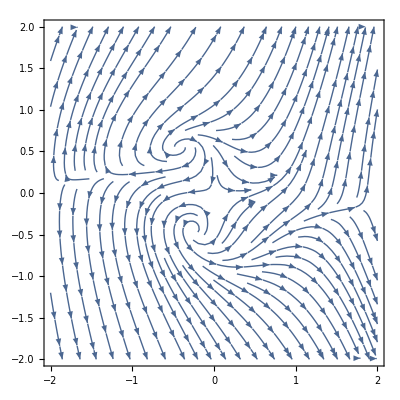

```mathematica
StreamPlot[newplot,{z,-2,2},{y,-2,2}](*Am I done here? *)
```

Going up to third order:

```mathematica
Fxyz3={{x y z (2 Π-2 ψ)+z^2 (2 Δ-Π-ψ)+y z ((Π-ψ)/2+1/2 (-Π+ψ))},{-2 x y^2 (Π-ψ)},{x^2 y (2 Π-2 ψ)+x z (2 Δ-Π-ψ)+y z (-Π+ψ)}};
```

```mathematica
{x12,ydot2,zdot2}=Λ.({{x}, {y}, {z}})+Fxyz3/.{x-> h2}
```

{{y z (a y^2+m y^3+b y z+k y^2 z+c z^2+l y z^2+n z^3) (2 Π-2 ψ)+z^2 (2 Δ-Π-ψ)+1/2 (a y^2+m y^3+b y z+k y^2 z+c z^2+l y z^2+n z^3) (2 Δ-Π-ψ)+y z ((Π-ψ)/2+1/2 (-Π+ψ))},{1/2 z (Π-ψ)-2 y^2 (a y^2+m y^3+b y z+k y^2 z+c z^2+l y z^2+n z^3) (Π-ψ)},{y (a y^2+m y^3+b y z+k y^2 z+c z^2+l y z^2+n z^3)^2 (2 Π-2 ψ)+z (a y^2+m y^3+b y z+k y^2 z+c z^2+l y z^2+n z^3) (2 Δ-Π-ψ)+1/2 y (-Π+ψ)+y z (-Π+ψ)}}

```mathematica
xdot2=1/2 x (2 Δ-Π-ψ)/.x-> h2;
```

```mathematica
Fullfxn=Expand[-xdot2+D[h2,y]*ydot+zdot*D[h2,z]];
Fullfxn/.{a-> 0,b-> 0,c-> 0,n-> 0,m-> 0,l-> 0,k-> 0}(*Check for non-zero coefficients on the expansion*)
```

{0}

Now we can double check this:

```mathematica
({{xdot2}, {ydot2}, {zdot2}})/.{a-> 0,b-> 0,c-> 0,n-> 0,m-> 0,l-> 0,k-> 0}
```

{{0},{{1/2 z (Π-ψ)}},{{1/2 y (-Π+ψ)+y z (-Π+ψ)}}}

This is the same expression!

We have non-zero coefficients! See how we can solve:

```mathematica
P2in.({{F1}, {F2}, {F3}})/.{x-> h}
```

P2in.{{F1},{F2},{F3}}

```mathematica
F1hy=1/2 (z (z (2 Δ-Π-ψ)+y (Π-ψ))+2 y (a y^2+b y z+c z^2)^2 (-Π+ψ)+z (a y^2+b y z+c z^2) (-2 Δ+Π+2 y Π+ψ-2 y ψ))+1/2 (2 y (a y^2+b y z+c z^2)^2 (Π-ψ)+z (a y^2+b y z+c z^2) (2 Δ-Π+2 y Π-ψ-2 y ψ)+z (z (2 Δ-Π-ψ)+y (-Π+ψ)))
F2hy=2 y^2 (a y^2+b y z+c z^2) (-Π+ψ);
F3hy=1/2 (-z (z (2 Δ-Π-ψ)+y (Π-ψ))-2 y (a y^2+b y z+c z^2)^2 (-Π+ψ)-z (a y^2+b y z+c z^2) (-2 Δ+Π+2 y Π+ψ-2 y ψ))+1/2 (2 y (a y^2+b y z+c z^2)^2 (Π-ψ)+z (a y^2+b y z+c z^2) (2 Δ-Π+2 y Π-ψ-2 y ψ)+z (z (2 Δ-Π-ψ)+y (-Π+ψ)));
Collect[Expand[F3hy],y]
```

1/2 (z (z (2 Δ-Π-ψ)+y (Π-ψ))+2 y (a y^2+b y z+c z^2)^2 (-Π+ψ)+z (a y^2+b y z+c z^2) (-2 Δ+Π+2 y Π+ψ-2 y ψ))+1/2 (2 y (a y^2+b y z+c z^2)^2 (Π-ψ)+z (a y^2+b y z+c z^2) (2 Δ-Π+2 y Π-ψ-2 y ψ)+z (z (2 Δ-Π-ψ)+y (-Π+ψ)))

2 c z^3 Δ-c z^3 Π-c z^3 ψ+y^5 (2 a^2 Π-2 a^2 ψ)+y^4 (4 a b z Π-4 a b z ψ)+y^3 (2 b^2 z^2 Π+4 a c z^2 Π-2 b^2 z^2 ψ-4 a c z^2 ψ)+y^2 (2 a z Δ-a z Π+4 b c z^3 Π-a z ψ-4 b c z^3 ψ)+y (2 b z^2 Δ-z Π-b z^2 Π+2 c^2 z^4 Π+z ψ-b z^2 ψ-2 c^2 z^4 ψ)

```mathematica
Λ.({{x}, {y}, {z}})
```

{{1/2 x (2 Δ-Π-ψ)},{1/2 z (Π-ψ)},{1/2 y (-Π+ψ)}}

```mathematica
xdot=(h)* (Δ-Π/2-ψ/2);
ydot=1/2 z (Π-ψ)+0;
zdot=1/2 y (ψ-Π)+y*z(ψ-Π);
```

```mathematica
dhdy=D[h,y]
dhdz=D[h,z]
```

2 a y+b z

b y+2 c z

```mathematica
Fullfxn=Expand[-xdot+dhdy*ydot+dhdz*zdot];
Collect[Fullfxn,y]/.z-> 0
```

y^2 (-a Δ+(a Π)/2-(b Π)/2+(a ψ)/2+(b ψ)/2)

```mathematica
Collect[Fullfxn,z]/. y-> 0
Collect[Fullfxn,y]
```

z^2 (-c Δ+(b Π)/2+(c Π)/2-(b ψ)/2+(c ψ)/2)

-c z^2 Δ+1/2 b z^2 Π+1/2 c z^2 Π-1/2 b z^2 ψ+1/2 c z^2 ψ+y^2 (-a Δ+(a Π)/2-(b Π)/2-b z Π+(a ψ)/2+(b ψ)/2+b z ψ)+y (-b z Δ+a z Π+(b z Π)/2-c z Π-2 c z^2 Π-a z ψ+(b z ψ)/2+c z ψ+2 c z^2 ψ)

I can solve for the coefficients of the expansion:

```mathematica
Solve[-a Δ+(a Π)/2-(b Π)/2+(a ψ)/2+(b ψ)/2==0,b]
```

{{b→(-2 a Δ+a Π+a ψ)/(Π-ψ)}}

```mathematica
Solve[-2 Δ-c Δ+Π+(b Π)/2+(c Π)/2+ψ-(b ψ)/2+(c ψ)/2==0,b]
```

{{b→(4 Δ+2 c Δ-2 Π-c Π-2 ψ-c ψ)/(Π-ψ)}}

```mathematica
Solve[-b Δ+a  Π+(b  Π)/2-c  Π-a ψ+(b  ψ)/2+c  ψ==0,b]
```

{{b→(2 (a Π-c Π-a ψ+c ψ))/(2 Δ-Π-ψ)}}

```mathematica
Solve[-a Δ+(a Π)/2-(b Π)/2+(a ψ)/2+(b ψ)/2==0&&-2 Δ-c Δ+Π+(b Π)/2+(c Π)/2+ψ-(b ψ)/2+(c ψ)/2==0&&-b Δ+a  Π+(b  Π)/2-c  Π-a ψ+(b  ψ)/2+c  ψ==0,{a,b,c}]
```

{{a→-(4 (Π-ψ)^2)/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2),b→(4 (2 Δ-Π-ψ) (Π-ψ))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2),c→-(2 (4 Δ^2-4 Δ Π+3 Π^2-4 Δ ψ-2 Π ψ+3 ψ^2))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)}}

```mathematica
F2n=F2hy /.{a->-(4 (Π-ψ)^2)/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2),b->(4 (2 Δ-Π-ψ) (Π-ψ))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2),c->-(2 (4 Δ^2-4 Δ Π+3 Π^2-4 Δ ψ-2 Π ψ+3 ψ^2))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)};
F3n=F3hy /.{a->-(4 (Π-ψ)^2)/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2),b->(4 (2 Δ-Π-ψ) (Π-ψ))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2),c->-(2 (4 Δ^2-4 Δ Π+3 Π^2-4 Δ ψ-2 Π ψ+3 ψ^2))/(4 Δ^2-4 Δ Π+5 Π^2-4 Δ ψ-6 Π ψ+5 ψ^2)};
```

```mathematica
J1= ({{D[F2n+1/2 z (Π-ψ),y], D[F2n+1/2 z (Π-ψ),z]}, {D[F3n+1/2 y (-Π+ψ),y], D[F3n+1/2 y (-Π+ψ),z]}})/.{y-> 0,z-> 0}
```

{{0,(Π-ψ)/2},{1/2 (-Π+ψ),0}}

```mathematica
Eigenvalues[J1]
```

{1/2 ⅈ (Π-ψ),-1/2 ⅈ (Π-ψ)}

Let’s see if this works:

```mathematica
NSYS=({{F1hy}, {F2hy}, {F3hy}});
NJ3=NSYS/.{a-> 0, b-> 0, c-> -2}
```

{{1/2 (z (z (2 Δ-Π-ψ)+y (Π-ψ))+8 y z^4 (-Π+ψ)-2 z^3 (-2 Δ+Π+2 y Π+ψ-2 y ψ))+1/2 (8 y z^4 (Π-ψ)-2 z^3 (2 Δ-Π+2 y Π-ψ-2 y ψ)+z (z (2 Δ-Π-ψ)+y (-Π+ψ)))},{-4 y^2 z^2 (-Π+ψ)},{1/2 (-z (z (2 Δ-Π-ψ)+y (Π-ψ))-8 y z^4 (-Π+ψ)+2 z^3 (-2 Δ+Π+2 y Π+ψ-2 y ψ))+1/2 (8 y z^4 (Π-ψ)-2 z^3 (2 Δ-Π+2 y Π-ψ-2 y ψ)+z (z (2 Δ-Π-ψ)+y (-Π+ψ)))}}

```mathematica
({{xdot}, {ydot}, {zdot}})
```

{{(a y^2+b y z+c z^2) (Δ-Π/2-ψ/2)},{1/2 z (Π-ψ)},{1/2 y (-Π+ψ)+y z (-Π+ψ)}}